# Zadanie 3.

```mathematica
solution = DSolve[{y'[x]+6y[x]==Cos[2x],y[0]==1},y[x],x]//Simplify
```

{{y[x]→1/20 (17 ⅇ^(-6 x)+3 Cos[2 x]+Sin[2 x])}}

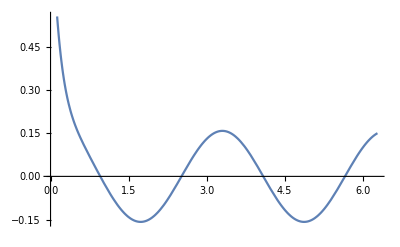

```mathematica
Plot[y[x]/.solution⟦1⟧,{x,0,2π}]
```